## Мухамадиев Владимир

# Задание 2

## Загрузка и предварительная обработка

```mathematica
(*Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.3.114 (February 14, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
data1=Import[NotebookDirectory[]<>"\\asoiaf-book1-edges.csv","CSV"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,2,Length[data1]}];
```

```mathematica
ew1=data1⟦2;;All,4⟧;
```

```mathematica
g1=Graph[el1,EdgeWeight->ew1];
```

```mathematica
data2=Import[NotebookDirectory[]<>"asoiaf-book2-edges.csv","CSV"];
```

```mathematica
el2=Table[data2⟦i,1⟧<->data2⟦i,2⟧,{i,2,Length[data2]}];
```

```mathematica
ew2=data2⟦2;;All,4⟧;
```

```mathematica
g2=Graph[el2,EdgeWeight->ew2];
```

```mathematica
data3=Import[NotebookDirectory[]<>"asoiaf-book3-edges.csv","CSV"];
```

```mathematica
el3=Table[data3⟦i,1⟧<->data3⟦i,2⟧,{i,2,Length[data3]}];
```

```mathematica
ew3=data3⟦2;;All,4⟧;
```

```mathematica
g3=Graph[el3,EdgeWeight->ew3];
```

```mathematica
data4=Import[NotebookDirectory[]<>"asoiaf-book4-edges.csv","CSV"];
```

```mathematica
el4=Table[data4⟦i,1⟧<->data4⟦i,2⟧,{i,2,Length[data4]}];
```

```mathematica
ew4=data4⟦2;;All,4⟧;
```

```mathematica
g4=Graph[el4,EdgeWeight->ew4];
```

```mathematica
data5=Import[NotebookDirectory[]<>"asoiaf-book5-edges.csv","CSV"];
```

```mathematica
el5=Table[data5⟦i,1⟧<->data5⟦i,2⟧,{i,2,Length[data5]}];
```

```mathematica
ew5=data5⟦2;;All,4⟧;
```

```mathematica
g5=Graph[el5,EdgeWeight->ew5];
```

```mathematica
gfullprep=Normal[GroupBy[{Flatten[{el1,el2,el3,el4,el5}],Flatten[{ew1,ew2,ew3,ew4,ew5}]}ᵀ,First->Last,Total]];
```

```mathematica
elfull=gfullprep⟦All,1⟧;
```

```mathematica
ewfull=gfullprep⟦All,2⟧;
```

```mathematica
gfull=Graph[elfull,EdgeWeight->ewfull];
```

```mathematica
RankedByCentrality[graph_,centralityfunction_]:=Transpose[Prepend[Transpose[ReverseSortBy[{VertexList[graph],centralityfunction[graph]}ᵀ,Last]],Range[VertexCount[graph]]]]
```

```mathematica
SetAttributes[RankedByCentrality,Listable]
```

## 1. Определите топ-10 персонажей по значению центральности по степени. Сколько среди них Старков?

```mathematica
topD=RankedByCentrality[{g1,g2,g3,g4,g5},DegreeCentrality];
```

```mathematica
topDfull=RankedByCentrality[gfull,DegreeCentrality];
```

```mathematica
topD⟦1,1;;10⟧
```

{{1,Eddard-Stark,66},{2,Robert-Baratheon,50},{3,Tyrion-Lannister,46},{4,Catelyn-Stark,43},{5,Jon-Snow,37},{6,Sansa-Stark,35},{7,Robb-Stark,35},{8,Bran-Stark,32},{9,Joffrey-Baratheon,30},{10,Cersei-Lannister,30}}

```mathematica
Length[Cases[topD⟦1,1;;10⟧,{_,x_String,_}/;StringContainsQ[x,"-Stark"]]]
```

5

## 2. Какое значение взвешенной степени у Eddard-Stark в сети?

```mathematica
WeightedDegreeCentrality[graph_]:=Total[Normal[WeightedAdjacencyMatrix[graph]]]
```

```mathematica
topWD=RankedByCentrality[{g1,g2,g3,g4,g5},WeightedDegreeCentrality];
```

```mathematica
topWDfull=RankedByCentrality[gfull,WeightedDegreeCentrality];
```

```mathematica
FirstCase[topWD⟦1⟧,{_,"Eddard-Stark",_}]⟦3⟧
```

1284

## 3. Сколько персонажей из топ-10, определенным по центральности по степени (из вопроса 1) осталось в топ-10 по взвешенной степени ?

```mathematica
Length[topD⟦1,1;;10,2⟧∩topWD⟦1,1;;10,2⟧]
```

8

## 4. Какой новый персонаж появился в топ-10 персонажей по значению центральности по посредничеству?

```mathematica
topB=RankedByCentrality[{g1,g2,g3,g4,g5},BetweennessCentrality];
```

```mathematica
topBfull=RankedByCentrality[gfull,BetweennessCentrality];
```

```mathematica
Complement[topB⟦1,1;;10,2⟧,topD⟦1,1;;10,2⟧∪topWD⟦1,1;;10,2⟧∩topB⟦1,1;;10,2⟧]
```

{Drogo}

## 5. Постройте топ-10 персонажей по значению центральности по посредничеству с учетом веса ребер. Кто теперь возглавляет список?

```mathematica
topBW=RankedByCentrality[{g1,g2,g3,g4,g5},IGBetweenness];
```

```mathematica
topBW⟦1,1,2⟧
```

Robert-Baratheon

## 6. Постройте топ-10 по значению PageRank. Какое место в топе занимает Daenerys-Targaryen?

```mathematica
topPRW=RankedByCentrality[{g1,g2,g3,g4,g5},IGPageRank];
```

```mathematica
topPRWfull=RankedByCentrality[gfull,IGPageRank];
```

```mathematica
topPRW⟦1,1;;10⟧
```

{{1,Eddard-Stark,0.072394},{2,Robert-Baratheon,0.0485173},{3,Jon-Snow,0.0477069},{4,Tyrion-Lannister,0.0436744},{5,Catelyn-Stark,0.034667},{6,Bran-Stark,0.0297742},{7,Robb-Stark,0.0292162},{8,Daenerys-Targaryen,0.0270896},{9,Sansa-Stark,0.0269618},{10,Cersei-Lannister,0.0216317}}

```mathematica
FirstCase[topPRW⟦1⟧,{_,"Daenerys-Targaryen",_}]⟦1⟧
```

8

## 7. Постройте рейтинг по значению центральности по степени для персонажей 5-ой книги. Какую теперь наивысшую строчку рейтинга занимает персонаж из Дома Старков?

```mathematica
topD⟦5,1;;10⟧
```

{{1,Jon-Snow,62},{2,Daenerys-Targaryen,58},{3,Stannis-Baratheon,47},{4,Tyrion-Lannister,33},{5,Theon-Greyjoy,33},{6,Cersei-Lannister,28},{7,Barristan-Selmy,25},{8,Hizdahr-zo-Loraq,22},{9,Asha-Greyjoy,18},{10,Melisandre,17}}

```mathematica
FirstCase[topD⟦5⟧,{_,x_String,_}/;StringContainsQ[x,"-Stark"]]⟦1⟧
```

21

## 8. Выберите персонажа и постройте график, показывающий как менялась его влиятельность от номера книги.

```mathematica
topEV=RankedByCentrality[{g1,g2,g3,g4,g5},EigenvectorCentrality];
```

```mathematica
topEVfull=RankedByCentrality[gfull,EigenvectorCentrality];
```

```mathematica
topWC=RankedByCentrality[{g1,g2,g3,g4,g5},ClosenessCentrality];
```

```mathematica
topWCfull=RankedByCentrality[gfull,ClosenessCentrality];
```

```mathematica
perIAB=VertexList[g1]∩VertexList[g2]∩VertexList[g3]∩VertexList[g4]∩VertexList[g5];
```

```mathematica
per=RandomChoice[perIAB]
```

Jeor-Mormont

```mathematica
RankedByName[top_,name_]:={Range[Length[top]],FirstCase[top[[#]],{_,name,_}]⟦1⟧&/@Range[Length[top]]}ᵀ
```

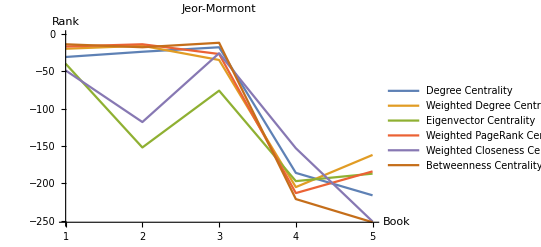

```mathematica
Module[{data=RankedByName[#,per]&/@{topD,topWD,topEV,topPRW,topWC,topB}},ListLinePlot[data,ScalingFunctions->"Reverse",AxesOrigin->{1,Max[Flatten[data,1]⟦All,2⟧]},PlotRange->{All,{1,Max[Flatten[data,1]⟦All,2⟧]}},AxesLabel->{"Book","Rank"},PlotLabel->per,PlotLegends->{"Degree Centrality","Weighted Degree Centrality","Eigenvector Centrality","Weighted PageRank Centrality","Weighted Closeness Centrality","Betweenness Centrality"}]]
```

## 9. Загрузите таблицу наиболее влиятельных персонажей, определенных по объединенной сети.

```mathematica
Grid[Prepend[Prepend[Partition[Flatten[SortBy[Table[{VertexList[gfull]⟦i⟧,(FirstCase[#,{_,VertexList[gfull]⟦i⟧,_}]&/@{topDfull,topWDfull,topEVfull,topPRWfull,topWCfull,topBfull})⟦All,1⟧},{i,1,VertexCount[gfull]}],Total[#⟦2⟧]&]⟦1;;10⟧],7],{SpanFromAbove,"Degree","Weighted Degree","Eigenvector","Weighted PageRank","Weighted Closeness","Betweenness"}],{"Name","Ranked By Centrality",SpanFromLeft}],Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray,2->Gray}}},Dividers->All,Spacings->{1, 1}]
```

Name | Ranked By Centrality |  |  |  |  | 
 | Degree | Weighted Degree | Eigenvector | Weighted PageRank | Weighted Closeness | Betweenness
Tyrion-Lannister | 1 | 1 | 1 | 2 | 7 | 2
Jaime-Lannister | 3 | 7 | 3 | 5 | 1 | 6
Cersei-Lannister | 4 | 3 | 2 | 3 | 8 | 7
Jon-Snow | 2 | 2 | 14 | 1 | 10 | 1
Stannis-Baratheon | 5 | 13 | 8 | 8 | 3 | 5
Eddard-Stark | 10 | 5 | 7 | 6 | 13 | 9
Robert-Baratheon | 14 | 10 | 6 | 13 | 2 | 10
Joffrey-Baratheon | 12 | 4 | 4 | 9 | 11 | 20
Arya-Stark | 6 | 11 | 11 | 7 | 20 | 8
Sansa-Stark | 7 | 8 | 5 | 12 | 19 | 13

```mathematica
Grid[Prepend[Transpose[Prepend[{topDfull⟦1,2;;3⟧,topWDfull⟦1,2;;3⟧,topEVfull⟦1,2;;3⟧,topPRWfull⟦1,2;;3⟧,topWCfull⟦1,2;;3⟧,topBfull⟦1,2;;3⟧}ᵀ,{"Degree","Weighted Degree","Eigenvector","Weighted PageRank","Weighted Closeness","Betweenness"}]],{"Centrality","№1","Value"}],Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray}}},Dividers->All,Spacings->{1, 1}]
```

Centrality | №1 | Value
Degree | Tyrion-Lannister | 122
Weighted Degree | Tyrion-Lannister | 2873
Eigenvector | Tyrion-Lannister | 0.0188473
Weighted PageRank | Jon-Snow | 0.0357054
Weighted Closeness | Jaime-Lannister | 0.0958755
Betweenness | Jon-Snow | 60635.8